```mathematica
ω[q_]:= √(1+10 q^2);
w[q_]:= √(1+20(1-Cos[q]));
```

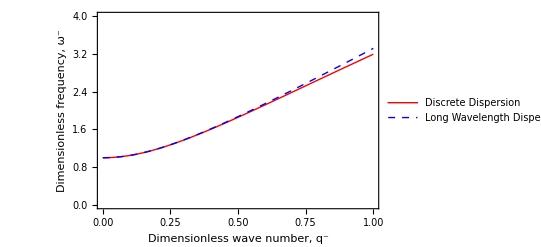

```mathematica
Plot[{w[q],ω[q]},{q,0,1},AspectRatio->1/GoldenRatio,FrameLabel->{"Dimensionless wave number, q^-","Dimensionless frequency, ω^-"},PlotRange->{0,4},Frame->True, PlotStyle->{Directive[Red],Directive[Blue, Dashed]},PlotLegends->Placed[{"Discrete  Dispersion","Long Wavelength  Dispersion"},{Left,Top}],BaseStyle->{FontFamily->"Times",14}]
```

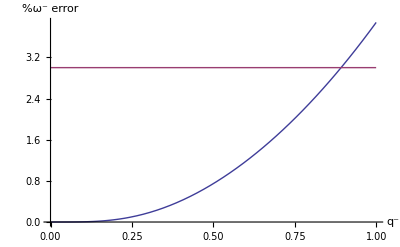

```mathematica
Plot[{100Abs[(w[q]-ω[q])/w[q]],3},{q,0,1},AxesLabel->{"q^-","%ω^- error"}]
```

```mathematica
100Abs[(w[0.85]-ω[0.85])/w[0.85]]
```

2.68601

```mathematica
ω[0.86]
```

2.89759